## Homework #1A: Introduction to Mathematica

### 1. Some ways of displaying information

1(a) Create a 20 by 30 matrix named rr of random numbers between zero and one.

```mathematica
rr = RandomReal[{0, 1}, {20, 30}];
```

1(b)  Display the matrix rr using MatrixForm.
>> This command will display the given array (2D array ‘rr’ for us) arranged as a regular matrix.

```mathematica
MatrixForm[rr]
```

(0.745945 | 0.928456 | 0.084657 | 0.724915 | 0.79125 | 0.721358 | 0.901712 | 0.711168 | 0.941853 | 0.142908 | 0.101097 | 0.962333 | 0.789118 | 0.282196 | 0.789963 | 0.950155 | 0.426064 | 0.0395891 | 0.787835 | 0.390535 | 0.547567 | 0.82154 | 0.572894 | 0.58384 | 0.790738 | 0.645331 | 0.14886 | 0.580005 | 0.0138956 | 0.746857
0.415587 | 0.735645 | 0.530165 | 0.506978 | 0.712216 | 0.760015 | 0.651455 | 0.688518 | 0.675955 | 0.321982 | 0.300083 | 0.612084 | 0.795148 | 0.449996 | 0.761817 | 0.119535 | 0.441788 | 0.663626 | 0.199239 | 0.403919 | 0.166951 | 0.730247 | 0.931906 | 0.959155 | 0.931961 | 0.175028 | 0.659788 | 0.429775 | 0.752089 | 0.42259
0.986292 | 0.943772 | 0.979676 | 0.124725 | 0.939479 | 0.648727 | 0.27479 | 0.480323 | 0.067007 | 0.0965465 | 0.179345 | 0.287042 | 0.789502 | 0.830959 | 0.61937 | 0.947025 | 0.424815 | 0.194574 | 0.574604 | 0.909737 | 0.732035 | 0.96509 | 0.387447 | 0.340163 | 0.37235 | 0.943989 | 0.648388 | 0.276605 | 0.801467 | 0.260988
0.560425 | 0.910895 | 0.69287 | 0.80183 | 0.768467 | 0.142145 | 0.785149 | 0.31859 | 0.807299 | 0.387232 | 0.0942954 | 0.721978 | 0.828356 | 0.491432 | 0.271465 | 0.773369 | 0.756813 | 0.248786 | 0.20397 | 0.747515 | 0.77533 | 0.650388 | 0.564209 | 0.840844 | 0.430248 | 0.223246 | 0.976589 | 0.830135 | 0.0123827 | 0.964414
0.609138 | 0.282541 | 0.985368 | 0.440559 | 0.0279402 | 0.710783 | 0.0552008 | 0.066546 | 0.864114 | 0.476453 | 0.141146 | 0.957336 | 0.267391 | 0.394828 | 0.0664724 | 0.280446 | 0.600757 | 0.323239 | 0.737324 | 0.971666 | 0.199072 | 0.343941 | 0.963107 | 0.0721629 | 0.929012 | 0.805502 | 0.669752 | 0.609633 | 0.925353 | 0.744436
0.493174 | 0.699157 | 0.0491696 | 0.412973 | 0.42516 | 0.999788 | 0.777196 | 0.487891 | 0.8452 | 0.328676 | 0.0994076 | 0.793613 | 0.869287 | 0.314137 | 0.372155 | 0.397929 | 0.683614 | 0.323624 | 0.0231881 | 0.279222 | 0.490412 | 0.42111 | 0.778903 | 0.444727 | 0.0715933 | 0.389211 | 0.0885559 | 0.25503 | 0.108399 | 0.839054
0.169711 | 0.234747 | 0.986873 | 0.0256418 | 0.306979 | 0.903862 | 0.734248 | 0.465804 | 0.587487 | 0.0153219 | 0.574588 | 0.766261 | 0.271373 | 0.495225 | 0.8855 | 0.0397379 | 0.369896 | 0.0826107 | 0.618425 | 0.323187 | 0.933946 | 0.463713 | 0.485546 | 0.972915 | 0.81036 | 0.0187625 | 0.0219359 | 0.809947 | 0.916524 | 0.0336321
0.652568 | 0.810352 | 0.0769032 | 0.124883 | 0.0350954 | 0.951846 | 0.448915 | 0.970233 | 0.523944 | 0.319592 | 0.994384 | 0.712425 | 0.570558 | 0.502904 | 0.487373 | 0.958009 | 0.241837 | 0.504916 | 0.0539111 | 0.283495 | 0.556599 | 0.136276 | 0.600387 | 0.0905882 | 0.983048 | 0.73506 | 0.172673 | 0.216215 | 0.184817 | 0.0114993
0.825745 | 0.41678 | 0.428444 | 0.986883 | 0.578736 | 0.394187 | 0.519705 | 0.776783 | 0.744037 | 0.772322 | 0.684818 | 0.327256 | 0.618895 | 0.819502 | 0.814755 | 0.119937 | 0.723802 | 0.952093 | 0.766688 | 0.004467 | 0.598289 | 0.752873 | 0.600239 | 0.964328 | 0.951551 | 0.827244 | 0.487673 | 0.511507 | 0.721817 | 0.318466
0.247539 | 0.624185 | 0.648069 | 0.0699725 | 0.938959 | 0.243448 | 0.462033 | 0.313414 | 0.136901 | 0.124063 | 0.732788 | 0.32678 | 0.650843 | 0.552877 | 0.834897 | 0.691189 | 0.69901 | 0.865602 | 0.164917 | 0.360748 | 0.0491093 | 0.0761448 | 0.466631 | 0.876306 | 0.109344 | 0.895208 | 0.299443 | 0.968258 | 0.400004 | 0.569834
0.290596 | 0.906767 | 0.448609 | 0.899476 | 0.195168 | 0.273123 | 0.99339 | 0.418054 | 0.841367 | 0.230329 | 0.972855 | 0.194755 | 0.245214 | 0.299973 | 0.86488 | 0.351423 | 0.298156 | 0.12338 | 0.246546 | 0.395237 | 0.994572 | 0.261278 | 0.290998 | 0.780777 | 0.463232 | 0.673201 | 0.965368 | 0.852072 | 0.696039 | 0.720825
0.892103 | 0.904871 | 0.873533 | 0.996039 | 0.0832044 | 0.480701 | 0.822082 | 0.160848 | 0.948188 | 0.101948 | 0.926587 | 0.0733876 | 0.0829701 | 0.298133 | 0.617345 | 0.51593 | 0.402092 | 0.892706 | 0.469418 | 0.485613 | 0.425961 | 0.0496985 | 0.17938 | 0.878495 | 0.614881 | 0.697636 | 0.756863 | 0.680484 | 0.620159 | 0.540544
0.876654 | 0.611532 | 0.0574947 | 0.705632 | 0.641807 | 0.316494 | 0.59005 | 0.382118 | 0.911968 | 0.386404 | 0.856971 | 0.0747602 | 0.390387 | 0.0754111 | 0.31722 | 0.925691 | 0.423474 | 0.246321 | 0.830109 | 0.854044 | 0.0257031 | 0.155829 | 0.791146 | 0.912368 | 0.484074 | 0.163015 | 0.986954 | 0.055744 | 0.985938 | 0.966768
0.360869 | 0.338917 | 0.347757 | 0.532605 | 0.272624 | 0.420627 | 0.0303553 | 0.153287 | 0.81727 | 0.947292 | 0.424504 | 0.0689247 | 0.983555 | 0.793815 | 0.901991 | 0.686466 | 0.429799 | 0.184784 | 0.6052 | 0.224178 | 0.197294 | 0.152641 | 0.063768 | 0.220113 | 0.677509 | 0.717555 | 0.911772 | 0.672613 | 0.406968 | 0.0723502
0.838505 | 0.363155 | 0.0673237 | 0.0465328 | 0.164407 | 0.435717 | 0.277338 | 0.554926 | 0.214762 | 0.192979 | 0.109644 | 0.468545 | 0.828695 | 0.197571 | 0.171234 | 0.418806 | 0.0230005 | 0.97438 | 0.757486 | 0.184551 | 0.435038 | 0.454113 | 0.673634 | 0.11507 | 0.952452 | 0.971346 | 0.282204 | 0.674985 | 0.000629815 | 0.438272
0.79217 | 0.266166 | 0.309677 | 0.787991 | 0.238711 | 0.312545 | 0.638945 | 0.637885 | 0.456668 | 0.471065 | 0.575778 | 0.786778 | 0.642914 | 0.204368 | 0.116709 | 0.228899 | 0.151757 | 0.928804 | 0.425279 | 0.630808 | 0.105792 | 0.98666 | 0.0673453 | 0.82158 | 0.920847 | 0.531625 | 0.240914 | 0.930344 | 0.292304 | 0.444769
0.330201 | 0.38289 | 0.689083 | 0.884309 | 0.865527 | 0.321234 | 0.969912 | 0.285981 | 0.49762 | 0.374204 | 0.654551 | 0.848371 | 0.106665 | 0.773166 | 0.908678 | 0.611211 | 0.127002 | 0.104465 | 0.818158 | 0.108202 | 0.850202 | 0.718754 | 0.294865 | 0.868805 | 0.582502 | 0.0404844 | 0.156802 | 0.906452 | 0.815018 | 0.8784
0.787007 | 0.0878511 | 0.975414 | 0.66289 | 0.92532 | 0.199003 | 0.280417 | 0.525398 | 0.920909 | 0.728153 | 0.0223075 | 0.831899 | 0.634308 | 0.883276 | 0.294494 | 0.221195 | 0.0835785 | 0.745274 | 0.370553 | 0.0315268 | 0.0632762 | 0.105496 | 0.893841 | 0.333664 | 0.611379 | 0.587229 | 0.537787 | 0.793697 | 0.708378 | 0.397814
0.12061 | 0.0584159 | 0.0280446 | 0.772482 | 0.692621 | 0.460692 | 0.507517 | 0.427167 | 0.625644 | 0.0153214 | 0.826298 | 0.73765 | 0.366681 | 0.987714 | 0.534944 | 0.771479 | 0.213786 | 0.681812 | 0.405973 | 0.0762545 | 0.0991838 | 0.861135 | 0.305688 | 0.905643 | 0.486164 | 0.115341 | 0.86409 | 0.816656 | 0.222158 | 0.36243
0.975818 | 0.164731 | 0.195309 | 0.106397 | 0.811904 | 0.162799 | 0.129434 | 0.258128 | 0.0452343 | 0.377812 | 0.480658 | 0.639756 | 0.38267 | 0.129093 | 0.267278 | 0.923717 | 0.20219 | 0.0891813 | 0.793484 | 0.531983 | 0.127563 | 0.869385 | 0.405786 | 0.291127 | 0.669095 | 0.538794 | 0.842679 | 0.681858 | 0.0826221 | 0.814489)

1(c) Display the matrix rr using ArrayPlot. 
>> Generates a plot where the values in the matrix input are plotted as a discrete array of squares (Grayscale by default). Here, a value closer to 1 is towards black and a value closer to 0 is towards white in a grayscale.

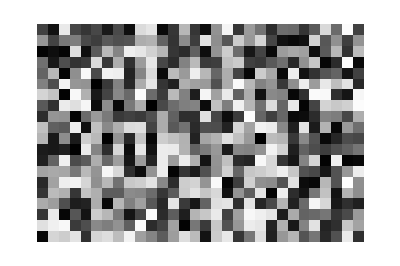

```mathematica
ArrayPlot[rr]
```

1 (d) Display the matrix rr using MatrixPlot
>> Similar to ArrayPlot, this gives a visual representation of the values in the matrix. By default it displays 0 values as white, with negative values tending to be bluish and positive values reddish.

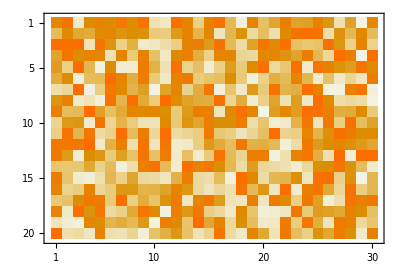

```mathematica
MatrixPlot[rr]
```

1 (e) Display the matrix rr using Image
>>  Creates an image with the pixel values given by the input. By default it displays the gray level from 0 (black) to 1 (white).

```mathematica
Image[rr]
```

-Graphics-

1(f) Display the matrix rr using ListPlot
>> ListPlot plots all the points given in the input matrix. “Joined” determines whether the points in the dataset are plotted as discrete points only or should also be joined in a line.

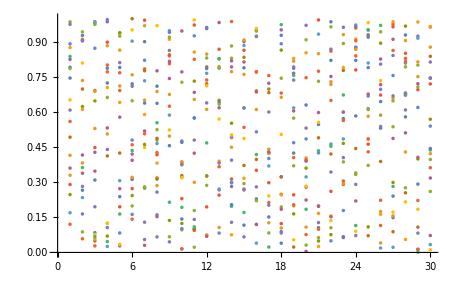

```mathematica
ListPlot[rr]
```

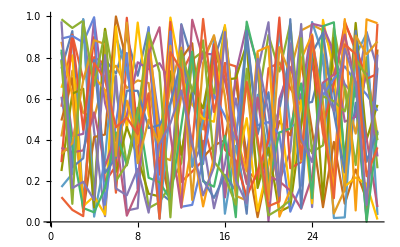

```mathematica
ListPlot[rr, Joined->True]
```

1(g) Display the matrix rr using ListPlot3D
>> 3D plot of the surface described by the input matrix. The height is the magnitude of the individual values in the matrix.

```mathematica
ListPlot3D[rr]
```

-Graphics3D-

1(h) Find another Mathematica plotting function, and use it to display rr
>> ListContourPlot: Generates a contour plot from the input array of values. Larger values (closer to 1) are shown lighter.

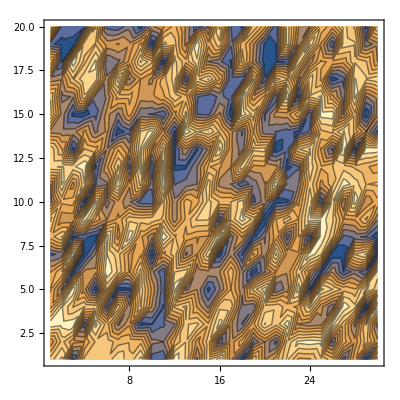

```mathematica
ListContourPlot[rr]
```

### 2. Dealing with Lists

2 (a)

```mathematica
a = {1, 2, x, y};
b = {5, z, 4, 3};

a+b
```

{6,2+z,4+x,3+y}

```mathematica
FullForm[a+b]
```

List[6,Plus[2,z],Plus[4,x],Plus[3,y]]

```mathematica
a*b
```

{5,2 z,4 x,3 y}

```mathematica
FullForm[a*b]
```

List[5,Times[2,z],Times[4,x],Times[3,y]]

```mathematica
a.b
```

5+4 x+3 y+2 z

```mathematica
FullForm[a.b]
```

Plus[5,Times[4,x],Times[3,y],Times[2,z]]

```mathematica
Sin[a+b]
```

{Sin[6],Sin[2+z],Sin[4+x],Sin[3+y]}

```mathematica
FullForm[Sin[a+b]]
```

List[Sin[6],Sin[Plus[2,z]],Sin[Plus[4,x]],Sin[Plus[3,y]]]

2 (b) Form a 2 by 4 matrix from a and b by m={a,b}. Display this matrix using
MatrixForm.

```mathematica
m={a,b};
MatrixForm[m]
```

(1 | 2 | x | y
5 | z | 4 | 3)

2 (c) Multiply the matrix m by the vector a.

```mathematica
MdotA = m.a
```

{5+x^2+y^2,5+4 x+3 y+2 z}

```mathematica
Dimensions[MdotA]
```

{2}

>> Dimensions of the dot product will be 2x1 as expected.

2 (d) Calculate m.a and m.b and combine them into a single list.

```mathematica
MdotB = m.b
```

{5+4 x+3 y+2 z,50+z^2}

```mathematica
MdotAB = {MdotA, MdotB}
```

{{5+x^2+y^2,5+4 x+3 y+2 z},{5+4 x+3 y+2 z,50+z^2}}

```mathematica
MdotABflat = Flatten[MdotAB]
```

{5+x^2+y^2,5+4 x+3 y+2 z,5+4 x+3 y+2 z,50+z^2}

2(d) Part II: Form a 3 by 4 Matrix whose first two rows are m, and whose third row 
is {m.a, m.b}.

```mathematica
Z = Join[m,{MdotABflat}]
```

{{1,2,x,y},{5,z,4,3},{5+x^2+y^2,5+4 x+3 y+2 z,5+4 x+3 y+2 z,50+z^2}}

```mathematica
MatrixForm[Z]
```

(1 | 2 | x | y
5 | z | 4 | 3
5+x^2+y^2 | 5+4 x+3 y+2 z | 5+4 x+3 y+2 z | 50+z^2)

2 (e) Form a 4 by 4 matrix whose first three rows are the same as in part (d) and whose 4th row is {1,2,3,4}. Call this matrix mParte.

```mathematica
mParte = Join[Z, {{1,2,3,4}}];
MatrixForm[mParte]
```

(1 | 2 | x | y
5 | z | 4 | 3
5+x^2+y^2 | 5+4 x+3 y+2 z | 5+4 x+3 y+2 z | 50+z^2
1 | 2 | 3 | 4)

2 (f) Find the determinant of mParte using Det.

```mathematica
determinantOfmParte = Det[mParte]
```

1335-573 x+82 x^2+6 x^3-186 y+47 x y-8 x^2 y+11 y^2+6 x y^2-8 y^3-224 z+80 x z-4 x^3 z+20 y z-4 x y z+3 x^2 y z-3 y^2 z-4 x y^2 z+3 y^3 z+38 z^2-10 x z^2-2 y z^2-3 z^3+x z^3

2 (g) Select from mParte the middle four elements, i.e., the 2nd and 3rd rows of the 2nd and third columns.

```mathematica
SelectedElements = {mParte[[2,2]], mParte[[2,3]], mParte[[3,2]], mParte[[3,3]] }
```

{z,4,5+4 x+3 y+2 z,5+4 x+3 y+2 z}

### 3. Interacting with the file system

3(a) Create a 20 by 30 matrix of random numbers between zero and one.

```mathematica
Mat = RandomReal[{0, 1}, {20, 30}];
```

3 (b) Let iR = Image[ yourRandomMatrix ] and display your image at different  sizes (100, 300, and 800) using the ImageSize option.

```mathematica
iR = Image[Mat];
Manipulate[Image[Mat, ImageSize->size],{size,{100,300,800}}]
```

3 (c) Save your image to a file in the .tif format using Export.
>> Note that this will create an image at the home directory of the user /home/<user>/.

```mathematica
Export["Image_Q3C.tif", iR];
```

3(d) Read your image back from the file using Import.

```mathematica
ImportediR = Import["Image_Q3C.tif"]
```

-Graphics-

3(e) Verify that the size/dimensions of the newly imported image and the original iR image are the same using ImageDimensions
>> “iR” is the generated image which is saved as “Image_Q3C.tif”, and ImportediR is the imported image. Note that they have the same dimensions.

```mathematica
ImageDimensions[iR]
```

{30,20}

```mathematica
ImageDimensions[ImportediR]
```

{30,20}

3(f) Verify that the size/dimensions of the newly imported image and the original iR image are the same using Dimensions. You can extract the raw data from the image using ImageData. What is the difference between the answers given by ImageDimensions from (e) and the answer you just got. Verify that the data is the same. Hint: Max[ Abs[ difference ] ] should be small.

```mathematica
Max[Abs[ImageData[iR]-ImageData[ImportediR]]]
```

7.62019×10^-6

The above shows that the data imported from the .tif image is very similar to the original image with minimal difference. Although the ImageDimensions are same, i.e. the number of pixels are same, but the precision of each pixel may have reduced slightly.

3(g) Now repeat the above (c)-(f) using the .gif format. Check the dimensions carefully. Explain how the .gif file is different.

```mathematica
Export["Image_Q3C.gif", iR];
iRGIF = Import["Image_Q3C.gif"]
```

-Graphics-

```mathematica
ImageDimensions[iR]
```

{30,20}

```mathematica
ImageDimensions[iRGIF]
```

{30,20}

```mathematica
Dimensions[ImageData[iRGIF]]
```

{20,30,3}

```mathematica
Max[Abs[ImageData[iR]-ImageData[iRGIF]]]
```

0.00195967

The above shows that the .gif data was stored differently (in 3 individual components) as compared to the .tif image. The imported .gif data was more different that the original image as compared to the imported .tif format image, which implies more loss in storage as compared to the .tif format.

3(h) Now repeat the above (c)-(f) using the .jpg format. Explain how the .jpg file is different.

```mathematica
Export["Image_Q3C.jpg", iR];
iRJPG = Import["Image_Q3C.jpg"]
```

-Graphics-

```mathematica
ImageDimensions[iRJPG]
```

{30,20}

```mathematica
Max[Abs[ImageData[iR]-ImageData[iRJPG]]]
```

0.161809

```mathematica
Dimensions[ImageData[iRJPG]]
```

{20,30}

The above shows that the imported .jpg data was more different that the original image as compared to the .tif format and the .gif formats both. This implies that the loss during conversion of raw data into .jpg and retrieving it back is higher than in the .tif and .gif formats.